# Coupling with adjustable torsional stiffness

## PROJECT

## External Forces

-Graphics-

```mathematica
eq1=Ra+Rb-m g-M1 g==0
```

-g m-g M1+Ra+Rb==0

```mathematica
eq2=M1 g posizione-Rb L+m g L/2==0
```

(g L m)/2+g M1 posizione-L Rb==0

```mathematica
solF=Solve[{eq1,eq2},{Rb,Ra}][[1]]
```

{Rb→-(-g L m-2 g M1 posizione)/(2 L),Ra→-(-g L m-2 g L M1+2 g M1 posizione)/(2 L)}

## K calculation

### K shaft torsion

M = k teta -> Mz=G teta/L Ip

```mathematica
kShaftBefore =(G Jshaft)/position;
```

```mathematica
kShaftAfter=(G Jshaft)/(L-position);
```

### k beam torsion

```mathematica
kBeamBefore =(G Jbeam)/position;
```

```mathematica
kBeamAfter =(G Jbeam)/(L-position);
```

### K in function of the parameters of the problem

Parametri :
>> ρ : density (always the same)
>> Rext: external radius of the flange linked to the motor at the beginning of the system
>> spessore1: thickness of the flange linked to the motor at the beginning of the system
>> Rint: radius of the cross section of the shaft
>> lenghtb: lenght of beams
>> I3: Momentum of inertia of third body (body linked then our mechanism)
>>distb: distance of beams from the center
>>spesb: width of the beam along y axis

```mathematica
m=Mshaft+3*M1;
```

```mathematica
M1=ρ Pi Rext^2 spessore1;
```

```mathematica
I1=0.5*M1(Rext^2);
```

```mathematica
I2=I1;
```

```mathematica
Mshaft=ρ Pi Rint^2 (L-2spessore1);
```

```mathematica
Jshaft=0.5*Mshaft(Rint^2)
```

1.5708 Rint^4 (L-2 spessore1) ρ

```mathematica
Jbeam=num*∫_distb^(distb+spesb) ∫_(-lenghtb/2)^(lenghtb/2) L ρ (x^2+y^2)ⅆxⅆy;
```

```mathematica
Ip=Jbeam+Jshaft+I1+I2+I3;
Ix=Ip/2;
Iy=Ix;
```

#### Numeric values of the parameters

```mathematica
lenghtb=2;
Rint=1.2;
spesb=1.5;
distb=1.3;
L=3;
spessore1 =0.1;
ρ=100;
G=10^6;
I3=1;
Rext=1.9;
num=6;
max=50;
g=9.81;
```

## FdT

-Graphics-

```mathematica
ex1=I1 teta1''[t]==M[t]-kShaftBefore (teta2[t]-teta1[t])-kBeamBefore(teta2[t]-teta1[t]);
ex2=I2 teta2''[t]==kShaftBefore (teta2[t]-teta1[t])+kBeamBefore(teta2[t]-teta1[t])-kShaftAfter (teta3[t]-teta2[t])-kBeamAfter(teta3[t]-teta2[t]);
ex3=I3 teta3''[t]==kShaftAfter (teta3[t]-teta2[t])+kBeamAfter(teta3[t]-teta2[t]);
```

```mathematica
eqs=Block[{lenghtb=1,Rint=1,spesb=1,distb=1,L=3,spessore1 =1,ρ=1,G=1,I3=1,Rext=1,num=1,max=5},LaplaceTransform[{ex1,ex2,ex3},t,s]/.teta1[0]->0/.teta1'[0]->0/.teta2[0]->0/.teta2'[0]->0/.teta3[0]->0/.teta3'[0]->0];
```

```mathematica
sols=Solve[eqs,{LaplaceTransform[teta1[t],t,s],LaplaceTransform[teta2[t],t,s],LaplaceTransform[teta3[t],t,s]}];
```

```mathematica
FdT1=Coefficient[LaplaceTransform[teta1[t],t,s]/.sols,LaplaceTransform[M[t],t,s]][[1]];
FdT2=Coefficient[LaplaceTransform[teta2[t],t,s]/.sols,LaplaceTransform[M[t],t,s]][[1]];
FdT3=Coefficient[LaplaceTransform[teta3[t],t,s]/.sols,LaplaceTransform[M[t],t,s]][[1]];
FdT={FdT1,FdT2,FdT3};
```

```mathematica
poles1=Quiet[Solve[Denominator[FdT1]==0,s]];
poles2=Quiet[Solve[Denominator[FdT2]==0,s]];
poles3=Quiet[Solve[Denominator[FdT3]==0,s]];
poles={poles1,poles2,poles3};
```

```mathematica
zeros1=Quiet[Solve[Numerator[FdT1]==0,s]];
zeros2=Quiet[Solve[Numerator[FdT2]==0,s]];
zeros3=Quiet[Solve[Numerator[FdT3]==0,s]];
zeros={zeros1,zeros2,zeros3};
```

#### Mass and Stiffness Matrix

```mathematica
MassMatrix={{I1,0,0},{0,I2,0},{0,0,I3}};
MatrixForm[MassMatrix]
```

(204.708 | 0 | 0
0 | 204.708 | 0
0 | 0 | 1)

```mathematica
StiffnessMatrix={{Coefficient[Expand[ex1[[2]]],teta1[t]], Coefficient[Expand[ex1[[2]]],teta2[t]], Coefficient[Expand[ex1[[2]]],teta3[t]]}, {Coefficient[Expand[ex2[[2]]],teta1[t]], Coefficient[Expand[ex2[[2]]],teta2[t]], Coefficient[Expand[ex2[[2]]],teta3[t]]},{Coefficient[Expand[ex3[[2]]],teta1[t]], Coefficient[Expand[ex3[[2]]],teta2[t]], Coefficient[Expand[ex3[[2]]],teta2[t]]}};
```

```mathematica
MatrixForm[StiffnessMatrix]
```

((2.6418×10^10)/position | -(2.6418×10^10)/position | 0
-(2.6418×10^10)/position | (2.6418×10^10)/(3-position)+(2.6418×10^10)/position | -(2.6418×10^10)/(3-position)
0 | -(2.6418×10^10)/(3-position) | -(2.6418×10^10)/(3-position))

k^-1 M u==u/w^2;

```mathematica
Di=Inverse[StiffnessMatrix.MassMatrix];
```

```mathematica
MatrixForm[Di]
```

((0.-(2.85736×10^23)/(3-position)^2-(1.42868×10^23)/((3-position) position))/(0.-(1.54525×10^36)/((3-position)^2 position)) | (0.-(1.42868×10^23)/((3-position) position))/(0.-(1.54525×10^36)/((3-position)^2 position)) | (0.+(1.42868×10^23)/((3-position) position))/(0.-(1.54525×10^36)/((3-position)^2 position))
(0.-(1.42868×10^23)/((3-position) position))/(0.-(1.54525×10^36)/((3-position)^2 position)) | (0.-(1.42868×10^23)/((3-position) position))/(0.-(1.54525×10^36)/((3-position)^2 position)) | (0.+(1.42868×10^23)/((3-position) position))/(0.-(1.54525×10^36)/((3-position)^2 position))
(0.+(2.92462×10^25)/((3-position) position))/(0.-(1.54525×10^36)/((3-position)^2 position)) | (0.+(2.92462×10^25)/((3-position) position))/(0.-(1.54525×10^36)/((3-position)^2 position)) | (0.+(2.92462×10^25)/((3-position) position))/(0.-(1.54525×10^36)/((3-position)^2 position)))

#### Transfer Diagrams

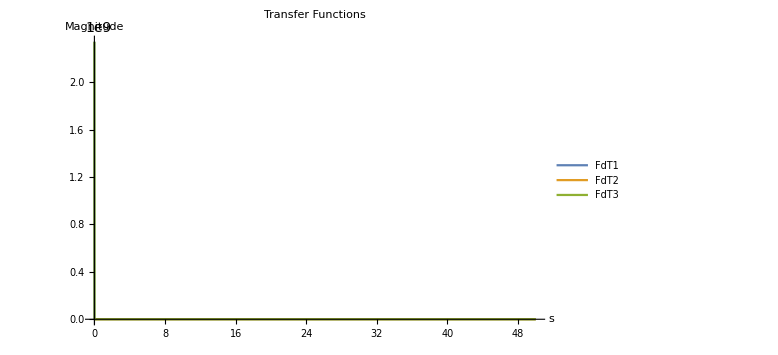

```mathematica
Block[{I3=11,max=50,position=2},Show[
Plot[FdT,{s,0,50},PlotStyle->Thick,PlotLabel->"Transfer Functions",PlotLegends->{"FdT1","FdT2","FdT3"},ImageSize->Large,AxesLabel->{"s","Magnitude"},PlotRange->All],
ParametricPlot[{(s/.poles[[1]][[4]])/I,t},{t,-max,max},PlotStyle->{Dashed,Red}]
]]
```

#### First Transfer function

We deduce the behaviour of the first transfer function estimating its parameters

```mathematica
Block[{I3=11,max=50,position=2},
Print["the first transfer function is: " ,FdT1];
Print[""];
Print["Its zeros are: " ,zeros[[1]]];
Print["Its values on the bode diagram are x[log(s)]: " ,Log[s/.zeros[[1]]]];
Print["Its poles are: " ,poles[[1]]];
Print["Its values on the bode diagram are x[log(s)]: " ,Log[s/.poles[[1]]]];
Print[""];
]
```

the first transfer function is: (0.00488501 (-4.39979×10^26+1.36872×10^19 s^2-1.06704×10^11 s^4+4. s^6))/((-1.29052×10^8+2. s^2) (6.83527×10^18 s^2-5.33522×10^10 s^4+2. s^6))

Its zeros are: {{s→-8032.82+2.27798×10^-9 ⅈ},{s→8032.82-2.27798×10^-9 ⅈ},{s→-8013.22-1.1083×10^-9 ⅈ},{s→8013.22+1.1083×10^-9 ⅈ},{s→-162934.-4.52141×10^-16 ⅈ},{s→162934.+4.52141×10^-16 ⅈ}}

Its values on the bode diagram are x[log(s)]: {8.99129+3.14159 ⅈ,8.99129-2.83585×10^-13 ⅈ,8.98885-3.14159 ⅈ,8.98885+1.38309×10^-13 ⅈ,12.0011-3.14159 ⅈ,12.0011+2.775×10^-21 ⅈ}

Its poles are: {{s→0.},{s→0.},{s→-8032.82},{s→8032.82},{s→-11346.2},{s→11346.2},{s→-162934.},{s→162934.}}

Its values on the bode diagram are x[log(s)]: {Indeterminate,Indeterminate,8.99129+3.14159 ⅈ,8.99129,9.33664+3.14159 ⅈ,9.33664,12.0011+3.14159 ⅈ,12.0011}

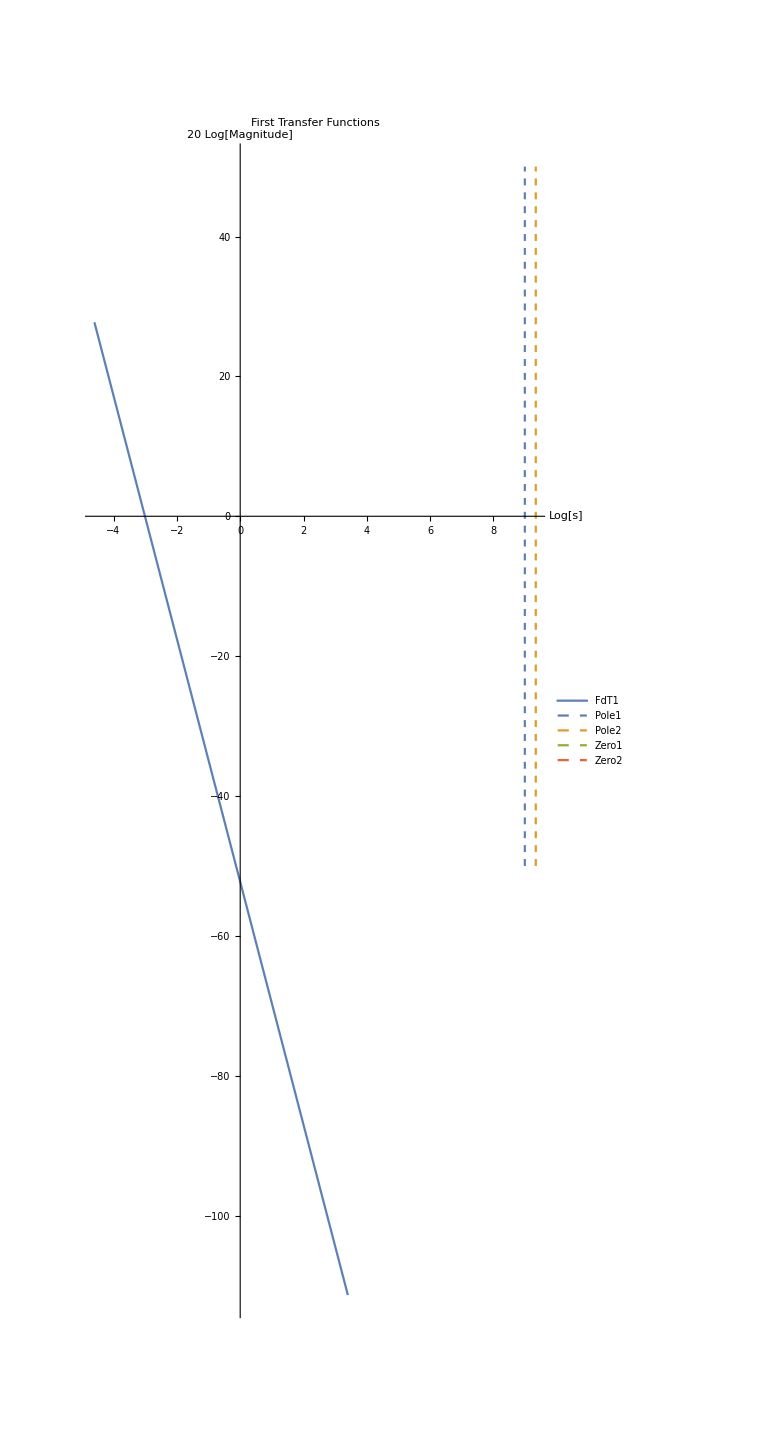

```mathematica
Block[{I3=11,max=50,position=2},Show[
ParametricPlot[{Log[s],20Log10[Abs[FdT[[1]]]]},{s,1/100,30},PlotRange->All,PlotStyle->Thick,PlotLabel->"First Transfer Functions",PlotLegends->{"FdT1","FdT2","FdT3"},ImageSize->Large,AxesLabel->{"Log[s]","20 Log[Magnitude]"},AspectRatio->Full,PlotRange->All],
ParametricPlot[{{(Log[s]/.poles[[1]][[4]]),t},{(Log[s]/.poles[[1]][[6]]),t},{(Log[s]/.zeros[[1]][[2]]),t},{(Log[s]/.zeros[[1]][[4]]),t}},{t,-max,max},PlotStyle->{Dashed},PlotLegends->{"Pole1","Pole2","Zero1","Zero2"}]
]]
```

#### Second Transfer function

We deduce the behaviour of the second transfer function estimating its parameters

```mathematica
Block[{I3=11,max=50,position=2},
Print["the second transfer function is: " ,FdT2];
Print[""];
Print["Its zeros are: " ,zeros[[2]]];
Print["Its values on the bode diagram are x[log(s)]: " ,Log[s/.zeros[[2]]]];
Print["Its poles are: " ,poles[[2]]];
Print["Its values on the bode diagram are x[log(s)]: " ,Log[s/.poles[[2]]]];
Print[""];
]
```

the second transfer function is: -(-3.48956×10^20+1.3209×10^10 s^2)/(-6.97912×10^20 (-1.3209×10^10+204.708 s^2)+(-2.6418×10^10+s^2) (-1.74478×10^20+(-3.9627×10^10+204.708 s^2) (-1.3209×10^10+204.708 s^2)))

Its zeros are: {{s→-162536.},{s→162536.}}

Its values on the bode diagram are x[log(s)]: {11.9987+3.14159 ⅈ,11.9987}

Its poles are: {{s→-162934.+1.55403×10^-13 ⅈ},{s→162934.-1.55403×10^-13 ⅈ},{s→-11346.2-5.81141×10^-10 ⅈ},{s→11346.2+5.81141×10^-10 ⅈ},{s→-0.000878721+0.00697813 ⅈ},{s→0.000878721-0.00697813 ⅈ}}

Its values on the bode diagram are x[log(s)]: {12.0011+3.14159 ⅈ,12.0011-9.53779×10^-19 ⅈ,9.33664-3.14159 ⅈ,9.33664+5.12188×10^-14 ⅈ,-4.95711+1.69606 ⅈ,-4.95711-1.44553 ⅈ}

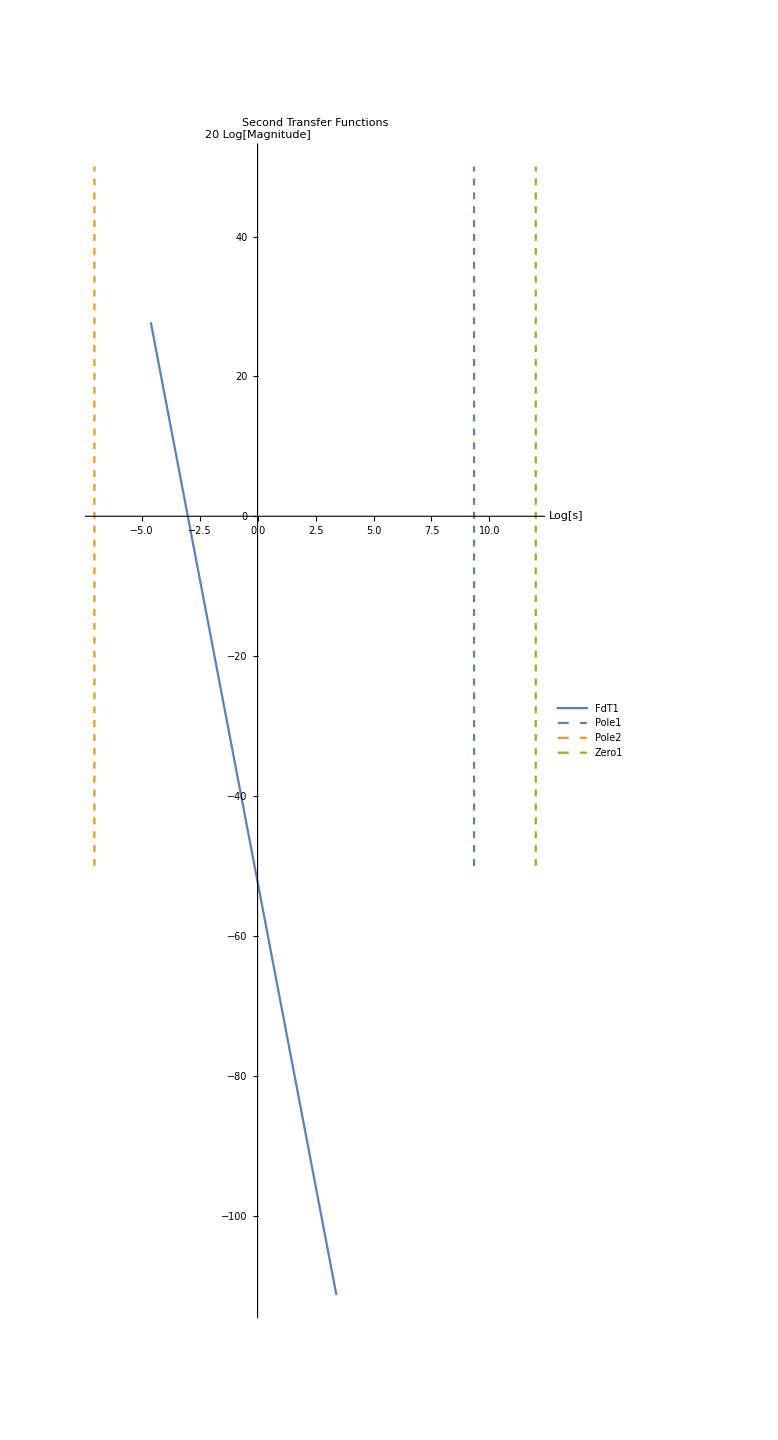

```mathematica
Block[{I3=11,max=50,position=2},Show[
ParametricPlot[{Log[s],20Log10[Abs[FdT[[2]]]]},{s,1/100,30},PlotRange->All,PlotStyle->Thick,PlotLabel->"Second Transfer Functions",PlotLegends->{"FdT1","FdT2","FdT3"},ImageSize->Large,AxesLabel->{"Log[s]","20 Log[Magnitude]"},AspectRatio->Full],
ParametricPlot[{{(Log[Re[s]]/.poles[[2]][[4]]),t},{(Log[Re[s]]/.poles[[2]][[6]]),t},{(Log[Re[s]]/.zeros[[2]][[2]]),t}},{t,-max,max},PlotStyle->{Dashed},PlotLegends->{"Pole1","Pole2","Zero1","Zero2"}]
]]
```

#### ThirdTransfer function

We deduce the behaviour of the third transfer function estimating its parameters

```mathematica
Block[{I3=11,max=50,position=2},
Print["the third transfer function is: " ,FdT3];
Print[""];
Print["Its zeros are: " ,zeros[[3]]];
Print["Its values on the bode diagram are x[log(s)]: " ,Log[s/.zeros[[3]]]];
Print["Its poles are: " ,poles[[3]]];
Print["Its values on the bode diagram are x[log(s)]: " ,Log[s/.poles[[3]]]];
Print[""];
]
```

the third transfer function is: (1.66545×10^16)/(6.83527×10^18 s^2-5.33522×10^10 s^4+2. s^6)

Its zeros are: {}

Its values on the bode diagram are x[log(s)]: Log[s]

Its poles are: {{s→0.},{s→0.},{s→-11346.2},{s→11346.2},{s→-162934.},{s→162934.}}

Its values on the bode diagram are x[log(s)]: {Indeterminate,Indeterminate,9.33664+3.14159 ⅈ,9.33664,12.0011+3.14159 ⅈ,12.0011}

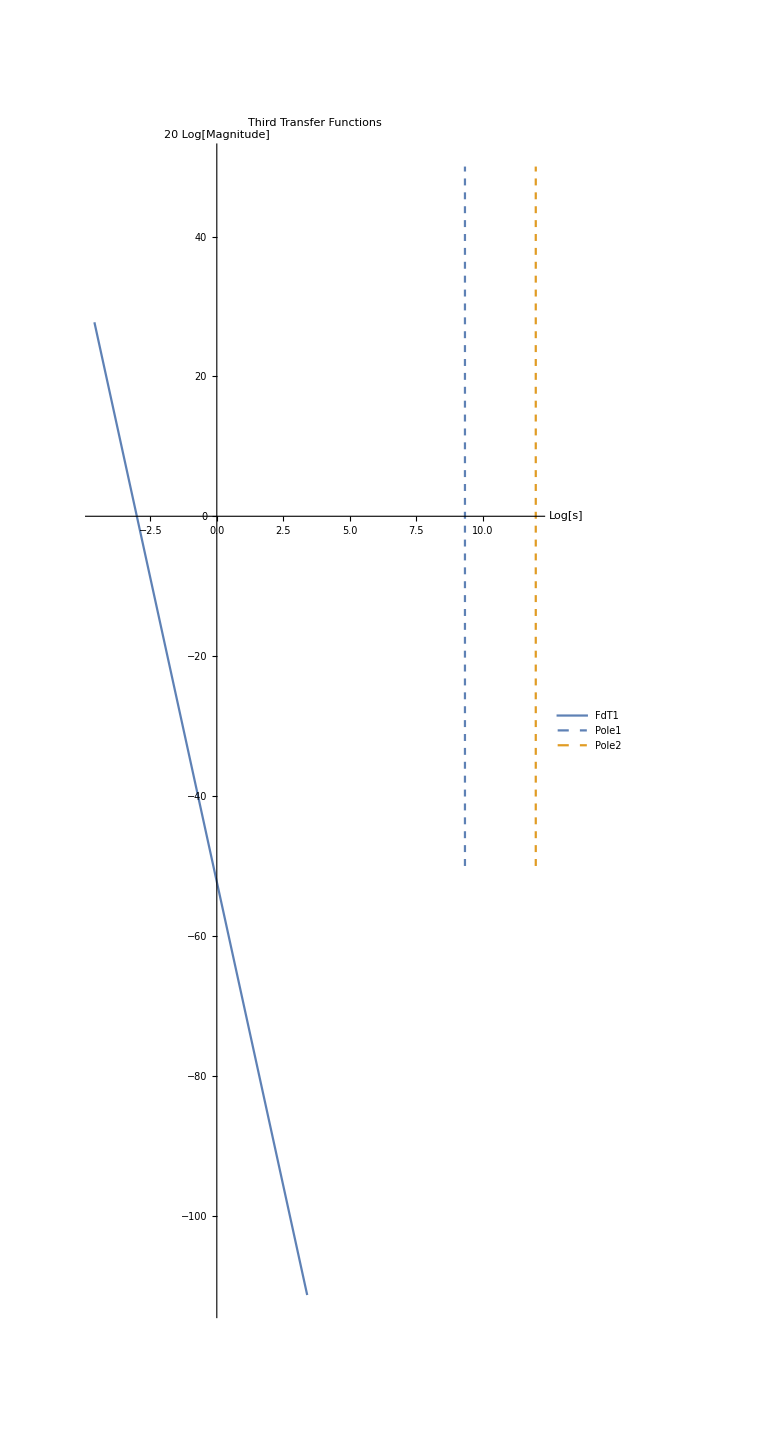

```mathematica
Block[{I3=11,max=50,position=2},Show[
ParametricPlot[{Log[s],20Log10[Abs[FdT[[3]]]]},{s,1/100,30},PlotRange->All,PlotStyle->Thick,PlotLabel->"Third Transfer Functions",PlotLegends->{"FdT1","FdT2","FdT3"},ImageSize->Large,AxesLabel->{"Log[s]","20 Log[Magnitude]"},AspectRatio->Full],
ParametricPlot[{{(Log[Re[s]]/.poles[[3]][[4]]),t},{(Log[Re[s]]/.poles[[3]][[6]]),t}},{t,-max,max},PlotStyle->{Dashed},PlotLegends->{"Pole1","Pole2","Zero1","Zero2"}]
]]
```

#### Total Transfer Function

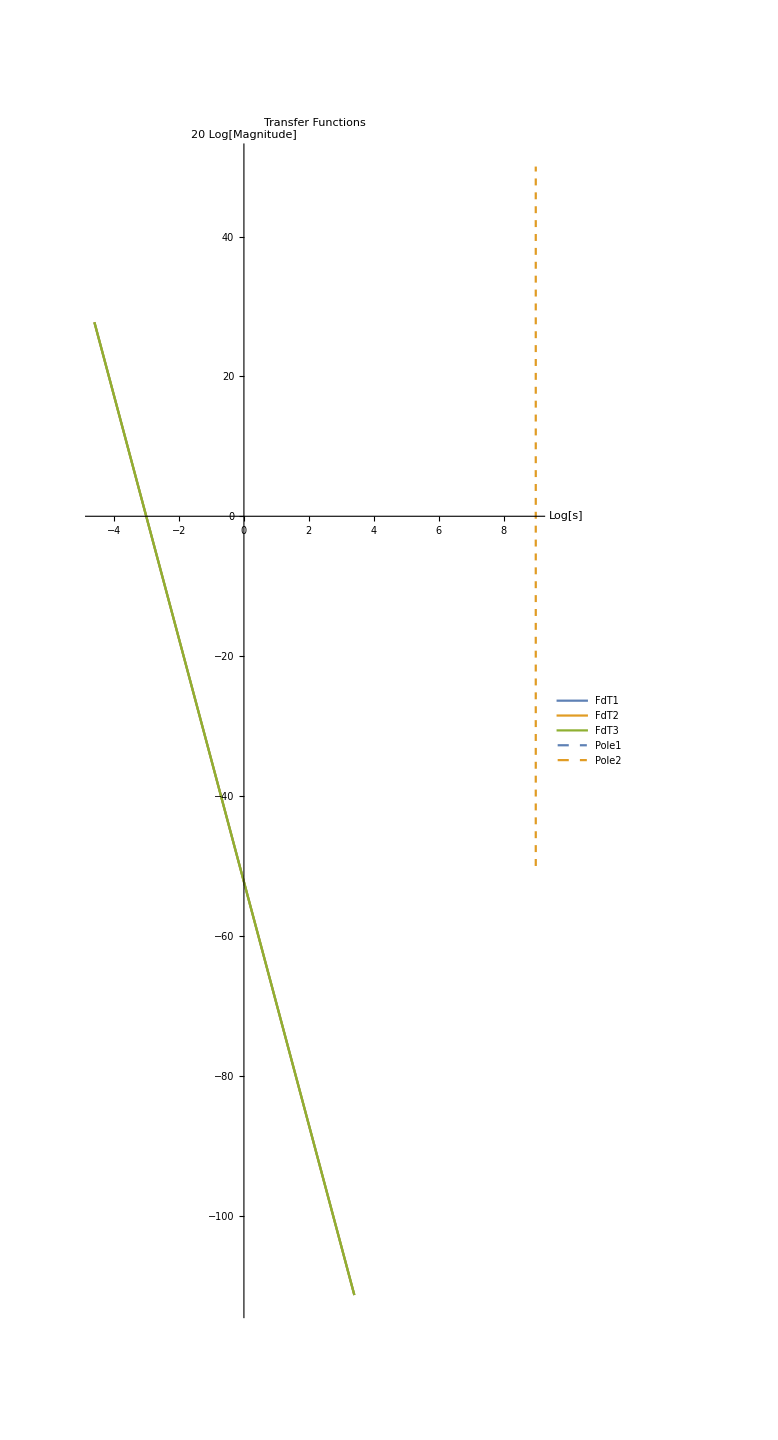

```mathematica
Block[{I3=11,position=4,max=50},Show[
ParametricPlot[{{Log[s],20Log10[Abs[FdT[[1]]]]},{Log[s],20Log10[Abs[FdT[[2]]]]},{Log[s],20Log10[Abs[FdT[[3]]]]}},{s,1/100,30},PlotRange->All,PlotStyle->Thick,PlotLabel->"Transfer Functions",PlotLegends->{"FdT1","FdT2","FdT3"},ImageSize->Large,AxesLabel->{"Log[s]","20 Log[Magnitude]"},AspectRatio->Full],
ParametricPlot[{{(Log[Re[s]]/.poles[[3]][[4]]),t},{(Log[Re[s]]/.poles[[3]][[6]]),t}},{t,-max,max},PlotStyle->{Dashed},PlotLegends->{"Pole1","Pole2","Zero1","Zero2"}]
]]
```

The poles are the same for all the three transfer function

## Azioni interne

### Ty

#### da x a L

```mathematica
Ty1=-Rb+m/L g (L-z)/.solF
```

1/6 (-47291.8-2225.13 posizione)+5254.64 (3-z)

#### da 0 a x

```mathematica
Ty2=-Rb+m/L g (L-z)+M g/.solF
```

9.81 M+1/6 (-47291.8-2225.13 posizione)+5254.64 (3-z)

#### Plot

```mathematica
fT=Piecewise[{{(Ty2/.posizione->position), z<=position}, {(Ty1/.posizione->position), z>position}}]
```

Piecewise[{{9.81 M+1/6 (-47291.8-2225.13 position)+5254.64 (3-z), z≤position}, {1/6 (-47291.8-2225.13 position)+5254.64 (3-z), z>position}, {0, True}}]

```mathematica
Manipulate[Block[{g=9.81},
Plot[Piecewise[{{(Ty2/.posizione->position), z<position}, {(Ty1/.posizione->position), z>position}}],{z,0,L},PlotStyle->Thick,PlotRange->{{0,L},{-200,200}}]
],{position,0,2}]
```

### Mx

#### da x a L

```mathematica
Mx1=Integrate[Ty1,z, GeneratedParameters->C]
```

7881.97 z-370.856 posizione z-2627.32 z^2+C[1]

```mathematica
c=Solve[(Mx1/.z->L)==0][[1]]
```

{C[1]→-3.63798×10^-12+1112.57 posizione}

```mathematica
Collect[Simplify[Mx1/.c],posizione]
```

-3.63798×10^-12+posizione (1112.57-370.856 z)+7881.97 z-2627.32 z^2

#### da 0 a x

```mathematica
Mx2=Integrate[Ty2,z, GeneratedParameters->C]
```

7881.97 z+9.81 M z-370.856 posizione z-2627.32 z^2+C[1]

```mathematica
c2=Solve[(Mx2/.z->0)==0][[1]]
```

{C[1]→0.}

```mathematica
Collect[Simplify[Mx2/.c2],posizione]
```

0.+7881.97 z+9.81 M z-370.856 posizione z-2627.32 z^2

#### Plot

```mathematica
fM=Piecewise[{{(Mx2/.c2/.posizione->position), z<position}, {(Mx1/.c/.posizione->position), z>=position}}]
```

Piecewise[{{0.+7881.97 z+9.81 M z-370.856 position z-2627.32 z^2, z<position}, {-3.63798×10^-12+1112.57 position+7881.97 z-370.856 position z-2627.32 z^2, z≥position}, {0, True}}]

```mathematica
Manipulate[Block[{g=9.81},
Plot[Piecewise[{{(Mx2/.c2/.posizione->position), z<position}, {(Mx1/.c/.posizione->position), z>position}}],{z,0,L},PlotStyle->Thick,PlotRange->{{0,L},{0,90}}]
],{position,0,2}]
```

we can find the maximum by means of the derivation

```mathematica
Solve[{D[fM,position]==0,D[fM,z]==0},{position,z}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{position→-21.2535,z→3.}}

Not finding a stationary point from the derivative of the gradient, we deduce that the maximum is on the edge of the function:

```mathematica
fM
```

Piecewise[{{0.+7881.97 z+9.81 M z-370.856 position z-2627.32 z^2, z<position}, {-3.63798×10^-12+1112.57 position+7881.97 z-370.856 position z-2627.32 z^2, z≥position}, {0, True}}]

```mathematica
fM[[1]][[1]][[1]]/.z->0
```

0.

It can’t be

```mathematica
fM[[1]][[2]][[1]]/.z->L
```

0.

It can’t be

It must be between the two functions

```mathematica
fM[[1]][[2]][[1]]/.z->position
```

-3.63798×10^-12+8994.53 position-2998.18 position^2

And its point of maximum is:

```mathematica
Solve[D[fM/.position->z,z]==0,z][[1]]
```

{z→1.5}

### Mz

```mathematica
Block[{lenghtb=1,Rint=1,spesb=1,distb=1,L=3,spessore1 =1,ρ=1,G=1,I3=1,Rext=1,num=1},MzInt=LaplaceTransform[M[t],t,s]-G Ip alpha z;
eqalpha1=alpha->(FdT2*LaplaceTransform[M[t],t,s]-FdT1*LaplaceTransform[M[t],t,s])/position;
eqalpha2=alpha->(FdT3*LaplaceTransform[M[t],t,s]-FdT2*LaplaceTransform[M[t],t,s])/(L-position);
MzIntTot=Simplify[Piecewise[{{(MzInt/.eqalpha1), z<=position}, {(MzInt/.eqalpha2), z>position}}]];
]
```

```mathematica
MzInt1=MzIntTot[[1]][[1]][[1]];
MzInt2=MzIntTot[[2]];
```

```mathematica
σ=((Mxcr/Ix)(distb+spesb))/.Mxcr->fM[[1]][[2]][[1]]/.z->position;
```

Apllying Von-Mises Theorem

```mathematica
σeq=√(σ^2+3 tau^2);
 σcr=80*10^6;
ϕ=1.4;
tau=MzMax/Ip(distb+spesb);
```

```mathematica
MzIntMax=Simplify[Solve[σcr==σeq ϕ,MzMax]];
```

```mathematica
solmax1=Solve[MzInt1==(MzMax/.MzIntMax)[[1]], LaplaceTransform[M[t],t,s]][[1]][[1]];
```

I have to find the minimum of the input to reach the critical internal moment

```mathematica
FindMinimum[Abs[LaplaceTransform[M[t],t,s]]/.solmax1,{position,z,s}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.000120507,{position→0.998309,z→-4.33052,s→-7.22694×10^-9}}